# Fractional Derivatives

Evan McIntire
12/02/2018

In Calculus, we start the study of derivatives with looking at the first, second, third, ..., nth derivative for n ∈ ℕ. We later expand this study to include anti-derivatives - which can be thought of as the negative first, second, third,... etc. derivative. Combined, they define the derivate operator d/dx on ℤ, and for many people that’s as far as the study of the operator goes.

But if we stop there, we’re not getting the full story - can we define d/dx for ℚ? For ℝ?

Let’s dive in and find out!

Exploring x^n and its derivatives

We start this study with x^n, due to the simplicity of it’s derivatives. As we know, d/dx x^n=nx^(n-1), d^2/dx^2 x^n=n(n-1)x^(n-2), and in general, d^a/dx^a x^n=(n!)/((n-a)!)x^(n-a). (Included below is a manipulate to confirm this behavior).

We have no issue for n > a, where n and a are both integers, but clearly we can’t take the factorial of a negative number, let alone a rational or real number. 

It seems we’re stuck, unless we can figure out what factorial looks like for those values.

```mathematica
Manipulate[D[x^n, {x, a}], {a, 0, 20, 1}, {n, 0, 20, 1}]
```

Enter Γ(z)

Lucky for us, such a generalization exists! It’s called the Gamma function, and we’ll take a quick look at it now.

If we think about how to generalize the factorial, it becomes a problem of interpolating the points (0, 0!), (1, 1!), (2, 2!), (3, 3!), ... etc.

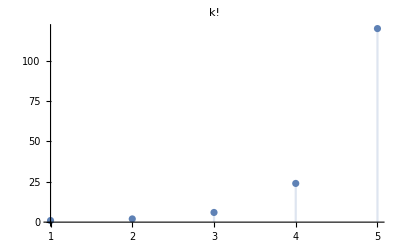

```mathematica
DiscretePlot[k!, {k, 1, 5}, PlotLabel->"k!"]
```

It should be clear that we can interpolate this, but it’s not obvious how, especially when it goes to infinity. 

Luckily, this work has already been done for us, by a lot of really talented mathematicians!

Thanks to them, we a formula for z with Re(z) > 0: Γ(z) = (∫_0)^∞x^(z-1)e^-x dx
Let’s see what it looks like:

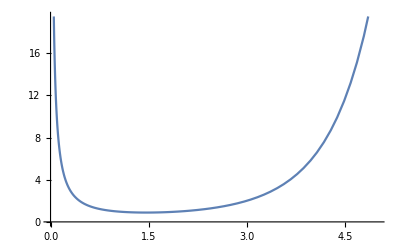

```mathematica
Plot[Gamma[z], {z, 0, 5}]
```

It seems to fit! Let’s double check and make sure the values are correct for the integers, and look at a few other values:

```mathematica
Grid[Join[{{"x", "Γ(x + 1)", "x!"}}, Table[{x, Gamma[x + 1], x!},{x, 1, 5}]], Frame->All]
Grid[
{{"x", "Γ(x + 1)"},
{0.5, Gamma[0.5 + 1]},
{1.5, Gamma[1.5 + 1]},
{1.75, Gamma[1.75 + 1]},
{1.95, Gamma[1.95 + 1]},
{2.01, Gamma[2.01 + 1]}
},Frame->All
]
```

x | Γ(x + 1) | x!
1 | 1 | 1
2 | 2 | 2
3 | 6 | 6
4 | 24 | 24
5 | 120 | 120

x | Γ(x + 1)
0.5 | 0.886227
1.5 | 1.32934
1.75 | 1.60836
1.95 | 1.91077
2.01 | 2.01858

There are a lot of other details we could unpack here, but for now let’s get back to our original topic.

Using Γ(x)

Now, we can taked^a/dx^a x^n=(n!)/((n-a)!)x^(n-a) and replace a with a real value α: d^α/dx^α x^n=(Γ(n+1))/(Γ(n-α + 1)!)x^(n-α)
Mathematica doesn’t have this built in, so let’s define it (for functions x^n):

```mathematica
FDXN[n_, a_] := (Gamma[n + 1]/Gamma[n -a + 1])*x^(n-a)
```

Lets plot it!

```mathematica
Animate[Plot[{x^2, 2x, 2, FDXN[2, a]},{x,0,5}, ImageSize->Large, PlotRange->Full, PlotLabel->"The fractional derivative of x^2 for a=[0, 2]"],{a,0,2},AnimationRunning->True, AnimationDirection->ForwardBackward]
```

It behaves...exactly as we might expect! Let’s do n = 5 to really drive it home.

```mathematica
Animate[Plot[{x^5, 5x^4,20x^3,60x^2,120x, 120,FDXN[5, a]},{x,0,5}, ImageSize->Large, PlotRange->Full, PlotLabel->"The fractional derivative of x^5 for a=[0, 5]"],{a,0,5},AnimationRunning->True, AnimationDirection->ForwardBackward]
```

Extending our definition

The derivative is linear, which means so is the fractional derivative! We’re going to want to take the derivative of more than just functions of the form x^n, so let’s write a function that does just that. Luckily, Mathematica makes rules like these really easy to define.

```mathematica
(* d/fx (f + g) = df/dx + dg/dx *)
FD1[f_+g_, a_] := FD1[f, a] + FD1[g, a]

(* d/dx (c*f) = c * (df/dx) *)
FD1[c_*f_, a_] := c*FD1[f,a]/;FreeQ[c,x]

(* d/dx (c) = 0 *)
FD1[c_, a_] := 0/;FreeQ[c, x]

(* Our definition from earlier! *)
FD1[x^n_., a_] := (Gamma[n + 1]/Gamma[n -a + 1])*x^(n-a)
```

Now FD should work for any polynomial! Let’s test, and then visualize.

```mathematica
f = x^2 + 2x +2;
g = x^9 -2x^5+32x-1;
Grid[{{"f", "D", "FD"},{f, D[f, {x}], FD1[f, 1]}, {g, D[g, {x}], FD1[g, 1]}}, Frame->All]
```

f | D | FD
2+2 x+x^2 | 2+2 x | 2+2 x
-1+32 x-2 x^5+x^9 | 32-10 x^4+9 x^8 | 32-10 x^4+9 x^8

Now that we’re sure it matches up, let’s visualize with some polynomials

```mathematica
Animate[With[{g=FD1[x^2 + 2x +2, a]}, Plot[{x^2 + 2x +2,2x+2,2, g},{x,0,3}, ImageSize->Large, PlotRange->{{0, 4},{0, 20}}, PlotLabel->"The fractional derivative of x^2+2x+2 for a=[0, 2]"]],{a,0,2},AnimationRunning->True, AnimationDirection->ForwardBackward]
```

Something is not quite right here!

As it turns out, we also have to change how we approach the derivative of a constant. We need some function such that FD[c, 1] = 0, and FD[c, 0] = c, and something to fill in the gaps.
Constant terms implicitly have an x^0  term, so from there we can define our fractional derivative of a constant:

```mathematica
(* Defs from before *)
FD[f_+g_, a_] := FD[f, a] + FD[g, a]
FD[c_*f_, a_] := c*FD[f,a]/;FreeQ[c,x]
FD[x^n_., a_] := (Gamma[n + 1]/Gamma[n -a + 1])*x^(n-a)

FD[c_, a_] := c*(Gamma[1]/Gamma[-a + 1])*x^(-a)/;FreeQ[c, x]
```

Now, trying again:

```mathematica
Animate[With[{g=FD[x^2 + 2x +2, a]}, Plot[{x^2 + 2x +2,2x+2,2, g},{x,0,3}, ImageSize->Large, PlotRange->{{0, 4},{0, 20}}, PlotLabel->"The fractional derivative of x^2+2x+2 for a=[0, 2]"]],{a,0,2},AnimationRunning->True, AnimationDirection->ForwardBackward]
```

Now it works as expected! But why does our fractional derivative approach ±∞ near the origin?

```mathematica
Grid[Join[{{"a", "expr"}}, Table[{a, FD[f, a]},{a, 1, 2, .1}]], Frame->All]
```

a | expr
1. | 2.+2. x^1.
1.1 | -0.187156/x^1.1+1.87156/x^0.1+2.07951 x^0.9
1.2 | -0.343575/x^1.2+1.71787/x^0.2+2.14734 x^0.8
1.3 | -0.46223/x^1.3+1.54077/x^0.3+2.20109 x^0.7
1.4 | -0.537204/x^1.4+1.34301/x^0.4+2.23835 x^0.6
1.5 | -0.56419/x^1.5+1.12838/x^0.5+2.25676 x^0.5
1.6 | -0.540989/x^1.6+0.901648/x^0.6+2.25412 x^0.4
1.7 | -0.467982/x^1.7+0.668546/x^0.7+2.22849 x^0.3
1.8 | -0.34852/x^1.8+0.43565/x^0.8+2.17825 x^0.2
1.9 | -0.189205/x^1.9+0.210227/x^0.9+2.10227 x^0.1
2. | 2.

Clearly, this is due to our Gamma function going into the negatives - what is happening there that we get this behavior, but it zeros out again at integers?

Back to Γ(z)

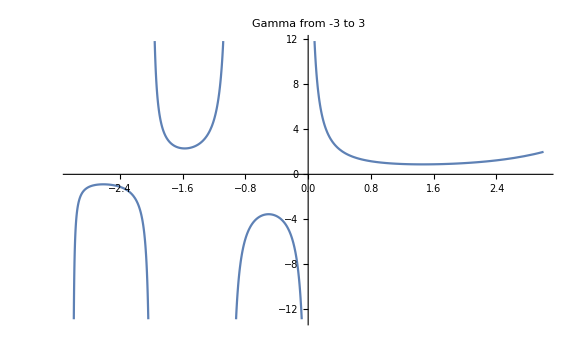

```mathematica
Plot[Gamma[z], {z, -3, 3}, ImageSize->Large, PlotLabel->"Gamma from -3 to 3"]
```

Now it’s clear! At the negative integers, gamma approaches plus or minus infinity, and because that term is in our denominator, it zeros out the term!

Taylor Polynomials

Now that we know we can take fractional derivatives of polynomials, we can use Taylor polynomials to extend this to any function and figure out a more closed-form solution!

Let’s start with e^x

```mathematica
q= Normal[Series[Exp[x],{x, 0, 50}]];
Animate[With[{g=FD[q, a]}, Plot[{e^x,q,  g},{x,0,4}, ImageSize->Large, PlotRange->{{0, 4},{0, 30}}, PlotLabel->"The fractional derivative of e^x for a=[0, 2]"]],{a,0,2},AnimationRunning->True, AnimationDirection->ForwardBackward]
```

No changes needed here! We’ll explicitly encode this relation at the end of the section.

```mathematica
r = Normal[Series[Exp[2x],{x, 0, 50}]];
Animate[With[{g=FD[r, a]}, Plot[{Exp[2x],2Exp[2x],4Exp[2x],  g},{x,0,4}, ImageSize->Large, PlotRange->{{0, 4},{0, 30}}, PlotLabel->"The fractional derivative of e^(2  x) for a=[0, 2]"]],{a,0,2},AnimationRunning->True, AnimationDirection->ForwardBackward]
```

All that's changing is the coefficient in the front - it appears to be 2^α

How about sin and cos?

```mathematica
s = Normal[Series[Sin[x],{x, 0, 50}]];
Animate[With[{g=FD[s, a]}, Plot[{Sin[x], Cos[x],  g},{x,0,4π}, ImageSize->Large, PlotRange->{{0, 4π},{-2, 2}}, PlotLabel->"The fractional derivative of sin(x) for a=[0, 2]"]],{a,0,2},AnimationRunning->True, AnimationDirection->ForwardBackward]
```

As we might have guessed, it’s just phase shifting! We can easily encode this relationship as well.

Buy why?

Why do all of this, other than to generalize?
According to Fractional PDEs: Theory, Algorithms and Applications (https://icerm.brown.edu/topical_workshops/tw18-4-fpde/)

“Fractional partial differential equations (FPDEs) are emerging as a powerful tool for modeling challenging multiscale phenomena including overlapping microscopic and macroscopic scales. Compared to integer-order PDEs, the fractional order of the derivatives in FPDEs may be a function of space and time or even a distribution, opening up great opportunities for modeling and simulation of multi-physics phenomena, e.g. seamless transition from wave propagation to diffusion, or from local to non-local dynamics.”

Unfortunately, tackling anything of this sort, even visually is a bit beyond the scope of this notebook.

That being said, the intuitive understanding of the derivative that we get from generalizing it is amazing, and there’s a lot of very interesting things to do in this area!